# Domača naloga – Mathematica

## 1. naloga

1. Izračunajte vsoto ∑_(k=1)^30 k^2/(k+5).
2. Rešite neenačbo:|x-1|≤ 2x+3 
3. Izračunajte drugi odvod funkcije  3tg (2cos(x)+1)  sin (x) in ga poenostavite.
4. S funkcijo FindRoot numerično izračunajte ničlo funkcije  (cos(x))/(e^(x^3-1)) z začetnim približkom x = 1 .

```mathematica
Sum[k^2/(k+5),{k,1,30}]

Reduce[Abs[x-1]<=2 x+3,x]

f[x_]:=3 Tan[2 Cos[x]+1] Sin[x]
D[f[x],{x,2}]//FullSimplify

FindRoot[Cos[x]/(Exp[x]-1)==0,{x,1}]
```

189870299151349/525103828704

x≥-2/3

-3 Sin[x] (Tan[1+2 Cos[x]]+2 Sec[1+2 Cos[x]]^2 (3 Cos[x]-4 Sin[x]^2 Tan[1+2 Cos[x]]))

{x→1.5708}

## 2. naloga

1. Definirajte funkciji x(t)=cos(5t) in y(t)=0.5 sin(t).
2. Poiščite take vrednosti t ∈ [0, π], da velja x(t)=0
3. Narišite parametrično podano krivuljo na območju t ∈[0,2π].

{{t→π/10},{t→(3 π)/10},{t→π/2},{t→(7 π)/10},{t→(9 π)/10}}

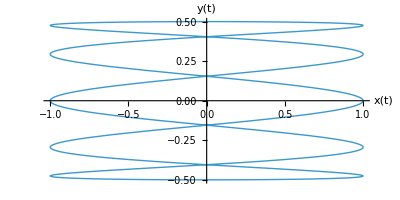

```mathematica
x[t_]:=Cos[5 t]
y[t_]:=1/2 Sin[t]

Solve[{Cos[5 t]==0,0<=t<=Pi},t]

ParametricPlot[{x[t],y[t]},{t,0,2 Pi},AxesLabel->{"x(t)","y(t)"},PlotStyle->Thick]
```